```mathematica
Quit[]
```

```mathematica
Uninstall[link]
```

/home/bednya/Work/c++/APIK/mr/math/mr

```mathematica
Quit[]
```

```mathematica
<<"mr_lib.m"
```

MR - Matching and Running Mathmatica interface

To see available functions use Names["mr`*"]

Andrey Pikelner <pikelner@theor.jinr.ru>

#### Old

```mathematica
s91=sol[PDG`MZ][]
```

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
s172=sol[PDG`MT][]
```

{gp→0.359473,g→0.649242,gs→1.16499,yt→0.961668,lam→0.128094,mu0→132.47,mu→173.21}

```mathematica
s91explmv = RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. s91,PDG`MZ]
```

{gp→0.3497 corr(h^2 (-0.00263351 as aw-0.00152161 aw^2)+0.0249616 aw h+1.,0.357008),g→0.652954 corr(h^2 (0.0000806233 as aw+0.000523887 aw^2)-0.00286806 aw h+1.,0.651477),gs→1.21442 corr(1.,1.21442),yb→0.165695 corr(h^2 (-0.0468244 as^2+0.000904795 as aw+0.000150551 aw^2)+h (-0.135054 as-0.00507558 aw)+1.,0.130054),yt→0.99743 corr(h^2 (-0.00288167 as^2-0.000487094 as aw+0.000619437 aw^2)+h (-0.000936964 as-0.00631505 aw)+1.,0.98599),lam→0.130315 corr(h^2 (-0.0218564 as aw-0.0208252 aw^2)+0.124333 aw h+1.,0.140956),ms→125.7 corr(h^2 (-0.00437885 as aw-0.00732411 aw^2)+0.0490884 aw h+1.,130.461),vev→246.22 corr(h^2 (0.00654936 as aw+0.00583444 aw^2)-0.0130843 aw h+1.,246.068),mu→91.1876 corr(1.,91.1876)}

{gp→0.00812283 √(8315.18 (-0.0010487 as aw h^2+0.00028118 aw^2 h^2+0.00667021 aw h+1)-6461.75 (0.000161247 as aw h^2+0.001056 aw^2 h^2-0.00573612 aw h+1)),g→0.652954 √(0.000161247 as aw h^2+0.001056 aw^2 h^2-0.00573612 aw h+1),gs→1.21442,yb→0.165695 √(-0.0317748 as^3 h^3-0.0754093 as^2 h^2+0.00318054 as aw h^2-0.270107 as h+0.000326863 aw^2 h^2-0.0101512 aw h+1),yt→0.99743 √(-0.00285811 as^3 h^3-0.00576247 as^2 h^2-0.000962354 as aw h^2-0.00187393 as h+0.00127875 aw^2 h^2-0.0126301 aw h+1),lam→0.130315 (-0.0218564 as aw h^2-0.0208252 aw^2 h^2+0.124333 aw h+1),ms→125.7 √(-0.00875771 as aw h^2-0.0122385 aw^2 h^2+0.0981768 aw h+1),vev→246.22 √(0.0130987 as aw h^2+0.0118401 aw^2 h^2-0.0261685 aw h+1),mu→91.1876}

{gp→0.00812283 √(8315.18 (-0.0010487 as aw h^2+0.00028118 aw^2 h^2+0.00667021 aw h+1)-6461.75 (0.000161247 as aw h^2+0.001056 aw^2 h^2-0.00573612 aw h+1)),g→0.652954 √(0.000161247 as aw h^2 lkkjлоk+0.001056 aw^2 h^2-0.00573612 aw h+1),gs→1.21442,yb→0.165695 √(-0.0317748 as^3 h^3-0.0754093 as^2 h^2+0.00318054 as aw h^2-0.270107 as h+0.000326863 aw^2 h^2-0.0101512 aw h+1),yt→0.99743 √(-0.00285811 as^3 h^3-0.00576247 as^2 h^2-0.000962354 as aw h^2-0.00187393 as h+0.00127875 aw^2 h^2-0.0126301 aw h+1),lam→0.130315 (-0.0218564 as aw h^2-0.0208252 aw^2 h^2+0.124333 aw h+1),ms→125.7 √(-0.00875771 as aw h^2-0.0122385 aw^2 h^2+0.0981768 aw h+1),vev→246.22 √(0.0130987 as aw h^2+0.0118401 aw^2 h^2-0.0261685 aw h+1),mu→91.1876}

{gp→0.3497 corr(h^2 (-0.00263351 as aw-0.00152161 aw^2)+h^3 (0.0000657368 as aw^2+0.0000379818 aw^3+0.)+0.0249616 aw h+1.,0.357008),g→0.652954 corr(h^2 (0.0000806233 as aw+0.000523887 aw^2)+h^3 (2.31232×10^-7 as aw^2+1.50254×10^-6 aw^3+0.)-0.00286806 aw h+1.,0.651477),gs→1.21442 corr(1.,1.21442),yb→0.165695 corr(h^2 (-0.0468244 as^2+0.000904795 as aw+0.000150551 aw^2)+h^3 (-0.0222112 as^3-0.000115465 as^2 aw+0.0000249248 as aw^2+7.64134×10^-7 aw^3)+h (-0.135054 as-0.00507558 aw)+1.,0.130054),yt→0.99743 corr(h^2 (-0.00288167 as^2-0.000487094 as aw+0.000619437 aw^2)+h^3 (-0.00143175 as^3-0.0000186543 as^2 aw-2.49563×10^-6 as aw^2+3.91177×10^-6 aw^3)+h (-0.000936964 as-0.00631505 aw)+1.,0.98599),lam→0.130315 corr(h^2 (-0.0218564 as aw-0.0208252 aw^2)+0.124333 aw h+1.,0.140956),ms→125.7 corr(h^2 (-0.00437885 as aw-0.00732411 aw^2)+h^3 (0.000214951 as aw^2+0.000359529 aw^3+0.)+0.0490884 aw h+1.,130.461),vev→246.22 corr(h^2 (0.00654936 as aw+0.00583444 aw^2)+h^3 (0.0000856936 as aw^2+0.0000763393 aw^3+0.)-0.0130843 aw h+1.,246.068),mu→91.1876 corr(1.,91.1876)}

{gp→0.3497 corr(h^2 (-0.00263351 as aw-0.00152161 aw^2)+0.0249616 aw h+1.,0.357008),g→0.652954 corr(h^2 (0.0000806233 as aw+0.000523887 aw^2)-0.00286806 aw h+1.,0.651477),gs→1.21442 corr(1.,1.21442),yb→0.165695 corr(h^2 (-0.0468244 as^2+0.000904795 as aw+0.000150551 aw^2)+h (-0.135054 as-0.00507558 aw)+1.,0.130054),yt→0.99743 corr(h^2 (-0.00288167 as^2-0.000487094 as aw+0.000619437 aw^2)+h (-0.000936964 as-0.00631505 aw)+1.,0.98599),lam→0.130315 corr(h^2 (-0.0218564 as aw-0.0208252 aw^2)+0.124333 aw h+1.,0.140956),ms→125.7 corr(h^2 (-0.00437885 as aw-0.00732411 aw^2)+0.0490884 aw h+1.,130.461),vev→246.22 corr(h^2 (0.00654936 as aw+0.00583444 aw^2)-0.0130843 aw h+1.,246.068),mu→91.1876 corr(1.,91.1876)}

```mathematica
yt
```

yt

```mathematica
s91ex = s91explmv /. z_ corr[x__,y_]:> y
```

{gp→0.357008,g→0.651477,gs→1.21442,yb→0.130054,yt→0.98599,lam→0.140956,ms→130.461,vev→246.068,mu→91.1876}

```mathematica
{Sqrt[2 lam vev^2 /. s91ex],ms /. s91ex, mu0 /. s91}
```

{130.651,130.461,130.852}

```mathematica
Sqrt[2 lam vev^2 /. s91ex]
```

130.651

```mathematica
s172explmv = RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. s172,PDG`MT]
```

{gp→0.3497 corr(h^2 (-0.00236713 as aw-0.00146392 aw^2)+0.0285632 aw h+1.,0.358383),g→0.652954 corr(h^2 (0.000259365 as aw+0.00087795 aw^2)-0.00855567 aw h+1.,0.648116),gs→1.16499 corr(1.,1.16499),yb→0.165695 corr(h^2 (-0.0507736 as^2+0.000802635 as aw+0.000124263 aw^2)+h (-0.146339 as-0.00408871 aw)+1.,0.1271),yt→0.99743 corr(h^2 (-0.00565514 as^2-0.00019768 as aw+0.000135448 aw^2)+h (0.000648939 aw-0.0229188 as)+1.,0.96769),lam→0.130315 corr(h^2 (-0.0103489 as aw-0.00262025 aw^2)-0.0114081 aw h+1.,0.127138),ms→125.7 corr(h^2 (-0.00392216 as aw-0.00749411 aw^2)+0.0606248 aw h+1.,131.961),vev→246.22 corr(h^2 (0.0012523 as aw-0.00578647 aw^2)+0.0663321 aw h+1.,261.503),mu→173.21 corr(1.,173.21)}

```mathematica
s172ex = s172explmv /. z_ corr[x__,y_]:> y
```

{gp→0.363337,g→0.636523,gs→1.02779,yb→0.118833,yt→0.916774,lam→0.0819254,ms→136.541,vev→340.44,mu→1732.1}

```mathematica
{Sqrt[2 lam vev^2 /. s172ex],ms /. s172ex, mu0 /. s172}
```

{137.805,136.541,136.12}

```mathematica
s172
```

{gp→0.359473,g→0.649242,gs→1.16499,yt→0.961668,lam→0.128094,mu0→132.47,mu→173.21}

```mathematica
s11=sol[100][]
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

```mathematica
test[scale_]:= Module[{ss= sol[scale][]},RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. ss,scale]]
```

```mathematica
TableForm[test[#] & /@ {100,130,160,190,210}]
```

{gp→0.00812283 √(8315.18 (-0.00283131 h^2+0.0117162 h+1)-6461.75 (0.00201106 h^2-0.0155796 h+1)),g→0.652954 √(0.00201106 h^2-0.0155796 h+1),gs→1.20692,yb→0.165695 √(0.00658846 h^2-0.0161523 h+1),yt→0.99743 √(0.00256054 h^2-0.0169405 h+1),lam→0.130315 (-0.0979513 h^2+0.228669 h+1),mu→100}->{gp→0.364622,g→0.648509,gs→1.20692,yb→0.164901,yt→0.990233,lam→0.14735,mu→100}

{gp→0.00812283 √(8315.18 (-0.00212488 h^2+0.00868233 h+1)-6461.75 (0.00274064 h^2-0.0203813 h+1)),g→0.652954 √(0.00274064 h^2-0.0203813 h+1),gs→1.18632,yb→0.165695 √(0.00446443 h^2-0.0100768 h+1),yt→0.99743 √(0.00154436 h^2-0.00583421 h+1),lam→0.130315 (-0.0635115 h^2+0.112998 h+1),mu→130}->{gp→0.365252,g→0.647169,gs→1.18632,yb→0.16523,yt→0.995289,lam→0.136764,mu→130}

{gp→0.00812283 √(8315.18 (-0.00153938 h^2+0.00627423 h+1)-6461.75 (0.00335482 h^2-0.0241922 h+1)),g→0.652954 √(0.00335482 h^2-0.0241922 h+1),gs→1.17077,yb→0.165695 √(0.00262894 h^2-0.00525457 h+1),yt→0.99743 √(0.000365003 h^2+0.00298102 h+1),lam→0.130315 (-0.0371799 h^2+0.0211874 h+1),mu→160}->{gp→0.365748,g→0.646115,gs→1.17077,yb→0.165478,yt→0.999098,lam→0.128231,mu→160}

{gp→0.00812283 √(8315.18 (-0.00103648 h^2+0.00427652 h+1)-6461.75 (0.00388828 h^2-0.0273533 h+1)),g→0.652954 √(0.00388828 h^2-0.0273533 h+1),gs→1.15836,yb→0.165695 √(0.00102204 h^2-0.00125419 h+1),yt→0.99743 √(-0.000827642 h^2+0.0102937 h+1),lam→0.130315 (-0.0163912 h^2-0.0549748 h+1),mu→190}->{gp→0.366158,g→0.645247,gs→1.15836,yb→0.165676,yt→1.00214,lam→0.121015,mu→190}

{gp→0.00812283 √(8315.18 (-0.00073577 h^2+0.00311115 h+1)-6461.75 (0.00420961 h^2-0.0291972 h+1)),g→0.652954 √(0.00420961 h^2-0.0291972 h+1),gs→1.15131,yb→0.165695 √(0.0000539779 h^2+0.00107943 h+1),yt→0.99743 √(-0.00160289 h^2+0.0145595 h+1),lam→0.130315 (-0.00481375 h^2-0.0994036 h+1),mu→210}->{gp→0.366397,g→0.644744,gs→1.15131,yb→0.165789,yt→1.00387,lam→0.116734,mu→210}

gp→0.3497 corr(-0.0112847 h^2+0.0534396 h+1.,0.364622) | g→0.652954 corr(0.000975192 h^2-0.00778978 h+1.,0.648509) | gs→1.20692 corr(1.,1.20692) | yb→0.165695 corr(0.00326162 h^2-0.00807613 h+1.,0.164901) | yt→0.99743 corr(0.0012444 h^2-0.00847024 h+1.,0.990233) | lam→0.130315 corr(-0.0979513 h^2+0.228669 h+1.,0.14735) | mu→100 corr(1,100)
gp→0.3497 corr(-0.0110567 h^2+0.0550045 h+1.,0.365252) | g→0.652954 corr(0.00131839 h^2-0.0101907 h+1.,0.647169) | gs→1.18632 corr(1.,1.18632) | yb→0.165695 corr(0.00221952 h^2-0.00503842 h+1.,0.16523) | yt→0.99743 corr(0.000767924 h^2-0.0029171 h+1.,0.995289) | lam→0.130315 corr(-0.0635115 h^2+0.112998 h+1.,0.136764) | mu→130 corr(1,130)
gp→0.3497 corr(-0.010883 h^2+0.0562458 h+1.,0.365748) | g→0.652954 corr(0.00160425 h^2-0.0120961 h+1.,0.646115) | gs→1.17077 corr(1.,1.17077) | yb→0.165695 corr(0.00131102 h^2-0.00262729 h+1.,0.165478) | yt→0.99743 corr(0.000181391 h^2+0.00149051 h+1.,0.999098) | lam→0.130315 corr(-0.0371799 h^2+0.0211874 h+1.,0.128231) | mu→160 corr(1,160)
gp→0.3497 corr(-0.0107432 h^2+0.057275 h+1.,0.366158) | g→0.652954 corr(0.00185061 h^2-0.0136767 h+1.,0.645247) | gs→1.15836 corr(1.,1.15836) | yb→0.165695 corr(0.000510823 h^2-0.000627095 h+1.,0.165676) | yt→0.99743 corr(-0.000427066 h^2+0.00514685 h+1.,1.00214) | lam→0.130315 corr(-0.0163912 h^2-0.0549748 h+1.,0.121015) | mu→190 corr(1,190)
gp→0.3497 corr(-0.0106634 h^2+0.0578751 h+1.,0.366397) | g→0.652954 corr(0.00199825 h^2-0.0145986 h+1.,0.644744) | gs→1.15131 corr(1.,1.15131) | yb→0.165695 corr(0.0000268433 h^2+0.000539715 h+1.,0.165789) | yt→0.99743 corr(-0.000827945 h^2+0.00727975 h+1.,1.00387) | lam→0.130315 corr(-0.00481375 h^2-0.0994036 h+1.,0.116734) | mu→210 corr(1,210)

```mathematica
RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. s11,100] //TableForm
```

{gp→0.364622,g→0.648509,gs→1.20692,yb→0.164901,yt→0.990233,lam→0.14735,mu→100}

gp→0.3497 corr(-0.0112847 h^2+0.0534396 h+1.)
g→0.652954 corr(0.000975192 h^2-0.00778978 h+1.)
gs→1.20692 corr(1.)
yb→0.165695 corr(0.00326162 h^2-0.00807613 h+1.)
yt→0.99743 corr(0.0012444 h^2-0.00847024 h+1.)
lam→0.130315 corr(-0.0979513 h^2+0.228669 h+1.)
mu→100 corr(1)

```mathematica
gs^2/(4 Pi) /. s91
```

0.117363

```mathematica
gs^2/(4 Pi) /. s172
```

0.108002

```mathematica
s172expl = RunParsFromPoleMassesAndAs[PDG`MZ,PDG`MW,PDG`MH,PDG`MT,PDG`GF,0.1080,PDG`MT]
```

{0.365963,0.645716,1.16498,1.00051,0.124907,173.21}

```mathematica
1/alpha[Sequence @@ s172expl[[;;2]]]
```

123.967

```mathematica
1/alpha[s91]
```

128.075

```mathematica
1/alpha[s91expl]
```

124.458

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
(%3-{0.368591,0.624226,0.925247,0.769222,0.0574923,139.558,20000})/{0.368591,0.624226,0.925247,0.769222,0.0574923,139.558,20000}
```

{3.96292×10^-7,-2.10725×10^-7,2.13605×10^-6,-1.73403×10^-6,0.0000155684,-0.0623822,0.}

```mathematica
?RunSM
```

RunSM[gp,g,gs,yt,lam,mu0,iscale,oscale] return running parameters at scale oscale given the values at scale iscale

```mathematica
Last /@ s91
```

{0.357258,0.651369,1.21442,0.986513,0.142474,130.852,91.1876}

```mathematica
RunSM[Sequence @@ Last /@ s91,20000]
```

{0.3685911460695877058,0.6242258684600446095,0.9252489763734841755,0.769220666148958078,0.05749319506139536593,130.8520648837378815,20000.}

```mathematica
RunSM[Sequence @@ Last /@ s91,2000]
```

{0.3636304896893455084,0.6354480651253094917,1.020833739374855457,0.8418795812594064327,0.08519739845856349741,130.8519048331099555,2000.}

```mathematica
Last /@ s91
```

{0.357258,0.651369,1.21442,0.986513,0.142474,130.852,91.1876}

```mathematica
gs^2/(4 Pi) /. s172
```

0.108002

```mathematica
ff[s_]:={mz=ScaleDependence[MZ][s],mw=ScaleDependence[MW][s],mt=ScaleDependence[MT][s],mh = ScaleDependence[MH][s],gf = ScaleDependence[GF][s]}
```

```mathematica
ff[s91];sol91 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

```mathematica
ff[s172];sol172 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

```mathematica
mz=ScaleDependence[MZ][s];
```

```mathematica
mw=ScaleDependence[MW][s];
```

```mathematica
mt=ScaleDependence[MT][s];
```

```mathematica
mh = ScaleDependence[MH][s];
gf = ScaleDependence[GF][s];
```

```mathematica
mz[PDG`MZ]
```

91.18759999999998696

```mathematica
mz[90]
```

91.21211134096251964

```mathematica
s91
```

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
x=sol[PDG`MZ][]
```

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
s90f91 = RunSM[Sequence @@ Last /@ x,90]
```

{0.3572316896928502406,0.6514383155590424857,1.215501494255514819,0.987314376414296246,0.1427973282174816497,130.8510956441278301,90.}

{0.3572216243975755818,0.651424777938606339,1.215501790959314502,0.9871359075077411136,0.1427828888003317188,130.8184659021347329,90.}

```mathematica
%34-%38
```

{-0.000010065295274659,-0.000013537620436147,2.96703799683×10^-7,-0.000178468906555132,-0.000014439417149931,-0.0326297419930972,0.}

```mathematica
MZp[Sequence @@ (Last /@ sol[90][])] /. aew->h /. as->h//Expand
```

{90.93694941255328966 √(-0.008549752653107084137 h^2+0.01406997352383323858 h+1.),-0.3909944942958736937 h^2+0.6397402352863936818 h+90.9369}

```mathematica
% /. h->1
```

{91.1876,91.1857}

```mathematica
MZp[Sequence @@ ReplacePart[(s90f91),-2->130.81846590213473291`19.116669051888564]] /. aew->h /. as->h//Expand
```

{90.93439678236903707 √(-0.00854978523725955559 h^2+0.01411245867391320973 h+1.),-0.3909986103269163238 h^2+0.6416539583142046931 h+90.9344}

```mathematica
% /. h->1
```

{91.187,91.1851}

```mathematica
MZp[Sequence @@ (Last /@ sol[PDG`MZ][])]/. aew->h /. as->h//Expand
```

{91.05451989989651426 √(-0.00871961895783104753 h^2+0.01164484115211933403 h+1.),-0.3985237595379080206 h^2+0.5301577102083918761 h+91.0545}

```mathematica
% /. h->1
```

{91.1876,91.1862}

```mathematica
PDG`MZ
```

91.1876

```mathematica
mz91=Table[{t,mz[t]},{t,90,400,10}]
```

```mathematica
Slot
```

```mathematica
sol91 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

```mathematica
sol91
```

({90,91.21211134096251964} | {100,91.01776924912738172} | {110,90.84715303634141556} | {120,90.69565892927843694} | {130,90.559884632547175} | {140,90.43724793696400894} | {150,90.32574479480431871} | {160,90.22379003724500788} | {170,90.13010914100913341} | {180,90.04366266045181524} | {190,89.96359220816225345} | {200,89.88918103399158249} | {210,89.81982472741833354} | {220,89.75500908599944513} | {230,89.6942931516855616} | {240,89.63729603773011782} | {250,89.58368657503299049} | {260,89.5331750866843509} | {270,89.48550678807077666} | {280,89.44045644295326808} | {290,89.39782400014370106} | {300,89.35743100319194678} | {310,89.31911761510499999} | {320,89.28274013546230441} | {330,89.24816891670896268} | {340,89.21528660461247434} | {350,89.18398664437925032} | {360,89.1541720060064656} | {370,89.12575409143838356} | {380,89.09865179336845553} | {390,89.07279068119559502} | {400,89.04810229412587447}
{90,80.4065383305876346} | {100,80.23581443827583561} | {110,80.08601060567656257} | {120,79.95304330492864797} | {130,79.83389854808601042} | {140,79.72629157209269202} | {150,79.62845117848448768} | {160,79.53897787487541386} | {170,79.45674756709620223} | {180,79.38084437510464528} | {190,79.31051264626322703} | {200,79.2451219645175054} | {210,79.18414116513429334} | {220,79.12711871982522408} | {230,79.07366771280108055} | {240,79.02345418202647739} | {250,78.97618796191307346} | {260,78.93161541300842062} | {270,78.88951359214308385} | {280,78.84968553488083019} | {290,78.81195640590299571} | {300,78.77617033321147814} | {310,78.74218778610580206} | {320,78.7098833882762828} | {330,78.67914408346206522} | {340,78.64986758727294494} | {350,78.62196107341533233} | {360,78.59534005326834993} | {370,78.569927415723341} | {380,78.54565260064136328} | {390,78.52245088429805119} | {400,78.500262759153414}
{90,125.7278568154980712} | {100,125.5067634418432021} | {110,125.3121631540220896} | {120,125.13887044825612} | {130,124.983048565342067} | {140,124.8417845905472738} | {150,124.7128185529946188} | {160,124.5943643474684677} | {170,124.4849876630156268} | {180,124.383520544577355} | {190,124.2890002054525245} | {200,124.200624314878531} | {210,124.1177177365213822} | {220,124.0397073888639366} | {230,123.966102971198157} | {240,123.8964819946445228} | {250,123.8304780206996273} | {260,123.7677713208339591} | {270,123.7080813862567242} | {280,123.6511608674012546} | {290,123.596790629634839} | {300,123.5447756887383063} | {310,123.4949418457969045} | {320,123.447132883167904} | {330,123.4012082130229692} | {340,123.3570408944224307} | {350,123.314515952155495} | {360,123.273528944145457} | {370,123.23398473488927} | {380,123.1957964405983645} | {390,123.1588845181709471} | {400,123.123175975241337}
{90,172.7902900721704301} | {100,172.2017490710214919} | {110,171.658464934784334} | {120,171.1543815416646482} | {130,170.6845010101870565} | {140,170.244677214232657} | {150,169.8314464338927309} | {160,169.4418930270279966} | {170,169.0735440443005562} | {180,168.7242866349545586} | {190,168.3923030761125112} | {200,168.0760193633113105} | {210,167.7740642478626232} | {220,167.4852363547660488} | {230,167.2084775908499555} | {240,166.9428514874346299} | {250,166.6875254320376584} | {260,166.4417559953476771} | {270,166.204876735988352} | {280,165.9762880029549093} | {290,165.7554483593253884} | {300,165.5418673301331036} | {310,165.335099239091863} | {320,165.1347379420143765} | {330,164.9404123101665256} | {340,164.7517823371339819} | {350,164.5685357692460911} | {360,164.3903851782542862} | {370,164.217065408527397} | {380,164.0483313429339865} | {390,163.8839559410146104} | {400,163.7237285107074623})

```mathematica
sol172 = {Table[{t,mz[t]},{t,90,400,10}],Table[{t,mw[t]},{t,90,400,10}],Table[{t,mh[t]},{t,90,400,10}],Table[{t,mt[t]},{t,90,400,10}]};
```

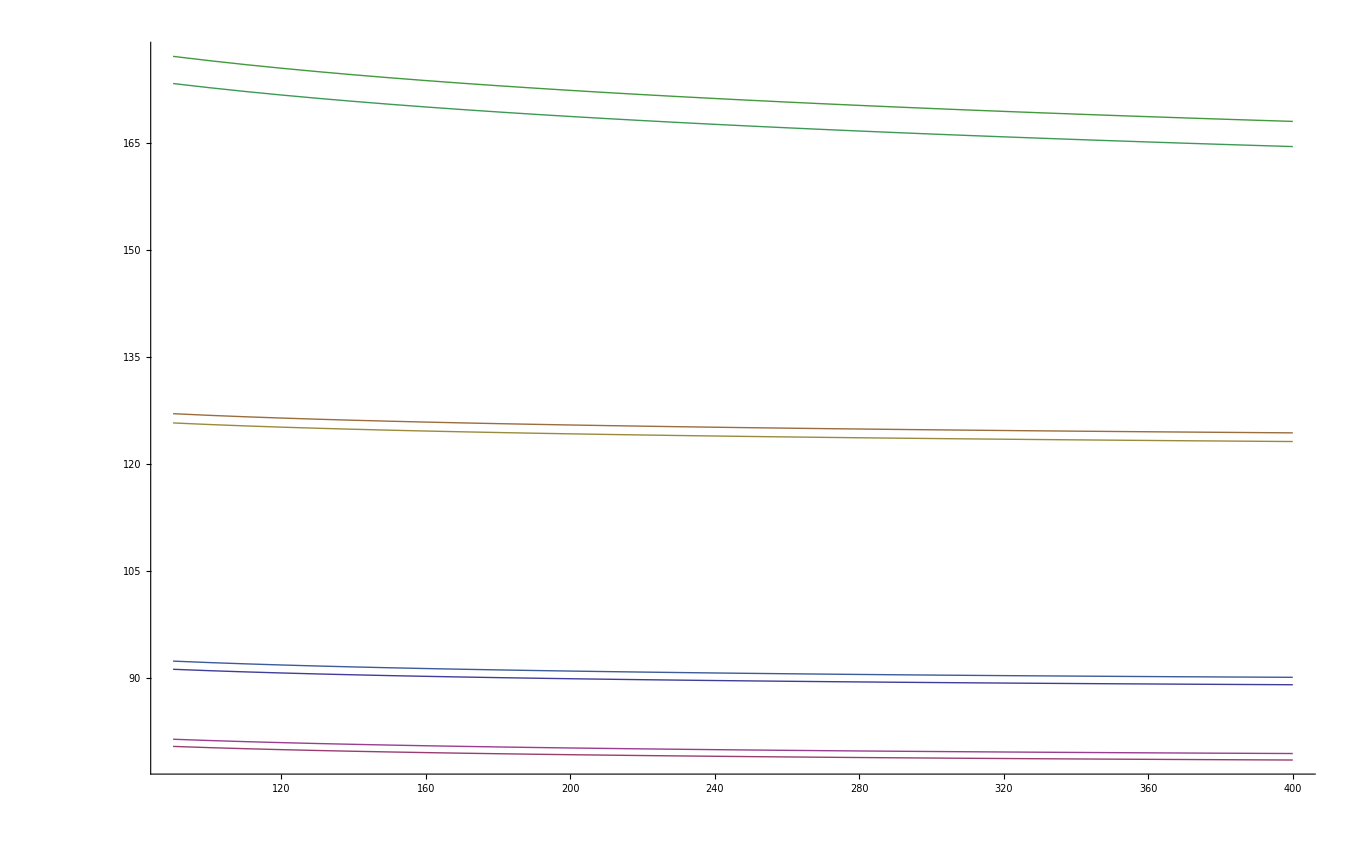

```mathematica
ListPlot[Join[sol91,sol172],Joined->True]
```

```mathematica
ScaleDependence[MZ]
```

```mathematica
k
```

```mathematica
ListPlot
```

### Difference between implicit and explicit determination of running parameters

```mathematica
Differe[scale_]:= Module[{soli = sol[scale][],sole},sole = RunParsFromPoleMassesAndAsWithMb[gs^2/(4 Pi) /. soli,scale]; soli = Last /@ soli; sole = Last /@ Delete[sole/. z_ corr[___,x_]:> x,{{4},{8}}];Most[(1-soli/sole)]]
```

```mathematica
OverAllDiff[scale_]:= Plus @@ Map[#^2 &,Differe[scale]]
```

```mathematica
scales = Table[10+5i,{i,0,58}];
```

```mathematica
scales = Table[90+2i,{i,0,105}]
```

{90,92,94,96,98,100,102,104,106,108,110,112,114,116,118,120,122,124,126,128,130,132,134,136,138,140,142,144,146,148,150,152,154,156,158,160,162,164,166,168,170,172,174,176,178,180,182,184,186,188,190,192,194,196,198,200,202,204,206,208,210,212,214,216,218,220,222,224,226,228,230,232,234,236,238,240,242,244,246,248,250,252,254,256,258,260,262,264,266,268,270,272,274,276,278,280,282,284,286,288,290,292,294,296,298,300}

```mathematica
scales = Table[10.0  10^(i /20),{i,0,40}]
```

{10.,11.2202,12.5893,14.1254,15.8489,17.7828,19.9526,22.3872,25.1189,28.1838,31.6228,35.4813,39.8107,44.6684,50.1187,56.2341,63.0957,70.7946,79.4328,89.1251,100.,112.202,125.893,141.254,158.489,177.828,199.526,223.872,251.189,281.838,316.228,354.813,398.107,446.684,501.187,562.341,630.957,707.946,794.328,891.251,1000.}

```mathematica
scales
```

{10.,11.2202,12.5893,14.1254,15.8489,17.7828,19.9526,22.3872,25.1189,28.1838,31.6228,35.4813,39.8107,44.6684,50.1187,56.2341,63.0957,70.7946,79.4328,89.1251,100.,112.202,125.893,141.254,158.489,177.828,199.526,223.872,251.189,281.838,316.228,354.813,398.107,446.684,501.187,562.341,630.957,707.946,794.328,891.251,1000.}

```mathematica
sslog = {#,Differe[#]}& /@ scales;
```

```mathematica
ss1 = {#,Differe[#]}& /@ scales
```

(90 | {-0.000676019,0.000185666,0.,-0.000759229,-0.0108155,-0.00299}
92 | {-0.000715713,0.000151952,0.,-0.00037747,-0.0107462,-0.00300118}
94 | {-0.000756862,0.000117346,0.,-0.0000141367,-0.0106773,-0.00301332}
96 | {-0.00079941,0.0000818571,0.,0.000331794,-0.0106086,-0.00302639}
98 | {-0.0008433,0.0000455019,0.,0.000661269,-0.0105401,-0.0030403}
100 | {-0.000888475,8.29742×10^-6,0.,0.00097517,-0.0104716,-0.00305501}
102 | {-0.000934881,-0.0000297367,0.,0.00127432,-0.0104031,-0.00307046}
104 | {-0.000982464,-0.0000685791,0.,0.00155947,-0.0103344,-0.00308661}
106 | {-0.00103117,-0.000108207,0.,0.00183134,-0.0102654,-0.0031034}
108 | {-0.00108095,-0.000148597,0.,0.00209059,-0.0101961,-0.00312081}
110 | {-0.00113175,-0.000189726,0.,0.00233785,-0.0101264,-0.00313878}
112 | {-0.00118352,-0.000231567,0.,0.00257369,-0.0100562,-0.00315729}
114 | {-0.00123622,-0.000274098,0.,0.00279865,-0.00998556,-0.00317629}
116 | {-0.0012898,-0.000317292,0.,0.00301326,-0.00991431,-0.00319576}
118 | {-0.00134422,-0.000361124,0.,0.00321798,-0.00984245,-0.00321566}
120 | {-0.00139942,-0.000405571,0.,0.00341328,-0.00976993,-0.00323597}
122 | {-0.00145538,-0.000450607,0.,0.00359956,-0.0096967,-0.00325667}
124 | {-0.00151205,-0.000496209,0.,0.00377724,-0.00962274,-0.00327772}
126 | {-0.0015694,-0.000542352,0.,0.00394668,-0.009548,-0.0032991}
128 | {-0.00162737,-0.000589013,1.11022×10^-16,0.00410825,-0.00947247,-0.0033208}
130 | {-0.00168595,-0.000636169,0.,0.00426227,-0.00939612,-0.00334279}
132 | {-0.00174509,-0.000683797,0.,0.00440907,-0.00931891,-0.00336504}
134 | {-0.00180476,-0.000731876,0.,0.00454894,-0.00924083,-0.00338756}
136 | {-0.00186493,-0.000780384,0.,0.00468218,-0.00916186,-0.0034103}
138 | {-0.00192556,-0.0008293,0.,0.00480903,-0.00908198,-0.00343327}
140 | {-0.00198663,-0.000878603,0.,0.00492977,-0.00900118,-0.00345644}
142 | {-0.00204811,-0.000928274,0.,0.00504464,-0.00891944,-0.00347981}
144 | {-0.00210996,-0.000978292,0.,0.00515385,-0.00883674,-0.00350334}
146 | {-0.00217217,-0.00102864,0.,0.00525764,-0.00875309,-0.00352705}
148 | {-0.0022347,-0.0010793,0.,0.0053562,-0.00866846,-0.0035509}
150 | {-0.00229753,-0.00113025,0.,0.00544974,-0.00858284,-0.00357489}
152 | {-0.00236063,-0.00118147,0.,0.00553844,-0.00849624,-0.00359901}
154 | {-0.00242399,-0.00123296,0.,0.00562249,-0.00840864,-0.00362325}
156 | {-0.00248757,-0.00128468,0.,0.00570204,-0.00832004,-0.0036476}
158 | {-0.00255136,-0.00133663,0.,0.00577727,-0.00823044,-0.00367204}
160 | {-0.00261533,-0.00138879,0.,0.00584832,-0.00813982,-0.00369657}
162 | {-0.00267947,-0.00144115,0.,0.00591536,-0.00804819,-0.00372119}
164 | {-0.00274375,-0.00149368,0.,0.00597851,-0.00795554,-0.00374587}
166 | {-0.00280815,-0.00154638,0.,0.00603791,-0.00786187,-0.00377062}
168 | {-0.00287266,-0.00159923,0.,0.0060937,-0.00776718,-0.00379543}
170 | {-0.00293726,-0.00165222,0.,0.00614599,-0.00767147,-0.00382029}
172 | {-0.00300193,-0.00170534,0.,0.00619491,-0.00757473,-0.0038452}
174 | {-0.00306665,-0.00175856,0.,0.00624057,-0.00747697,-0.00387014}
176 | {-0.0031314,-0.00181189,0.,0.00628307,-0.00737819,-0.00389511}
178 | {-0.00319618,-0.0018653,2.22045×10^-16,0.00632252,-0.00727839,-0.00392011}
180 | {-0.00326096,-0.00191879,0.,0.00635902,-0.00717757,-0.00394513}
182 | {-0.00332573,-0.00197234,0.,0.00639267,-0.00707573,-0.00397016}
184 | {-0.00339047,-0.00202595,1.11022×10^-16,0.00642355,-0.00697287,-0.0039952}
186 | {-0.00345517,-0.00207959,0.,0.00645176,-0.00686899,-0.00402025}
188 | {-0.00351982,-0.00213327,0.,0.00647738,-0.00676411,-0.0040453}
190 | {-0.0035844,-0.00218697,0.,0.00650049,-0.0066582,-0.00407034}
192 | {-0.00364891,-0.00224068,2.22045×10^-16,0.00652118,-0.00655129,-0.00409538}
194 | {-0.00371332,-0.00229439,0.,0.00653951,-0.00644338,-0.0041204}
196 | {-0.00377762,-0.00234809,0.,0.00655555,-0.00633446,-0.00414541}
198 | {-0.00384181,-0.00240178,0.,0.00656938,-0.00622454,-0.0041704}
200 | {-0.00390587,-0.00245544,0.,0.00658107,-0.00611362,-0.00419536}
202 | {-0.00396979,-0.00250906,0.,0.00659068,-0.00600171,-0.0042203}
204 | {-0.00403356,-0.00256264,0.,0.00659827,-0.00588881,-0.00424521}
206 | {-0.00409717,-0.00261617,0.,0.0066039,-0.00577492,-0.00427008}
208 | {-0.0041606,-0.00266963,1.11022×10^-16,0.00660764,-0.00566005,-0.00429492}
210 | {-0.00422386,-0.00272303,0.,0.00660953,-0.0055442,-0.00431972}
212 | {-0.00428692,-0.00277635,0.,0.00660962,-0.00542738,-0.00434448}
214 | {-0.00434978,-0.00282959,0.,0.00660798,-0.00530958,-0.00436919}
216 | {-0.00441243,-0.00288274,0.,0.00660466,-0.00519082,-0.00439386}
218 | {-0.00447486,-0.00293578,0.,0.00659969,-0.00507109,-0.00441848}
220 | {-0.00453705,-0.00298872,0.,0.00659313,-0.0049504,-0.00444304}
222 | {-0.00459901,-0.00304155,0.,0.00658502,-0.00482876,-0.00446755}
224 | {-0.00466073,-0.00309426,0.,0.00657541,-0.00470616,-0.00449201}
226 | {-0.00472219,-0.00314685,0.,0.00656434,-0.00458262,-0.0045164}
228 | {-0.00478338,-0.0031993,0.,0.00655185,-0.00445814,-0.00454074}
230 | {-0.0048443,-0.00325161,0.,0.00653798,-0.00433272,-0.00456502}
232 | {-0.00490495,-0.00330378,0.,0.00652277,-0.00420636,-0.00458923}
234 | {-0.0049653,-0.00335579,0.,0.00650625,-0.00407908,-0.00461337}
236 | {-0.00502537,-0.00340765,0.,0.00648847,-0.00395087,-0.00463745}
238 | {-0.00508513,-0.00345935,0.,0.00646945,-0.00382173,-0.00466146}
240 | {-0.00514458,-0.00351088,0.,0.00644923,-0.00369168,-0.00468539}
242 | {-0.00520371,-0.00356223,0.,0.00642784,-0.00356072,-0.00470926}
244 | {-0.00526253,-0.0036134,0.,0.00640532,-0.00342885,-0.00473305}
246 | {-0.00532101,-0.00366439,0.,0.00638169,-0.00329608,-0.00475677}
248 | {-0.00537916,-0.00371519,0.,0.00635699,-0.00316241,-0.0047804}
250 | {-0.00543696,-0.0037658,0.,0.00633124,-0.00302784,-0.00480397}
252 | {-0.00549441,-0.0038162,0.,0.00630448,-0.00289238,-0.00482745}
254 | {-0.00555151,-0.0038664,0.,0.00627672,-0.00275604,-0.00485085}
256 | {-0.00560825,-0.00391638,0.,0.006248,-0.00261881,-0.00487417}
258 | {-0.00566462,-0.00396616,0.,0.00621834,-0.00248071,-0.00489741}
260 | {-0.00572062,-0.00401571,0.,0.00618777,-0.00234173,-0.00492056}
262 | {-0.00577623,-0.00406504,0.,0.00615631,-0.00220188,-0.00494363}
264 | {-0.00583146,-0.00411414,0.,0.00612398,-0.00206117,-0.00496661}
266 | {-0.0058863,-0.004163,0.,0.00609081,-0.0019196,-0.0049895}
268 | {-0.00594075,-0.00421163,0.,0.00605682,-0.00177718,-0.00501231}
270 | {-0.00599479,-0.00426001,0.,0.00602203,-0.0016339,-0.00503503}
272 | {-0.00604843,-0.00430815,0.,0.00598646,-0.00148977,-0.00505765}
274 | {-0.00610165,-0.00435604,0.,0.00595014,-0.0013448,-0.00508019}
276 | {-0.00615445,-0.00440368,1.11022×10^-16,0.00591308,-0.00119899,-0.00510263}
278 | {-0.00620684,-0.00445105,2.22045×10^-16,0.0058753,-0.00105235,-0.00512498}
280 | {-0.00625879,-0.00449816,0.,0.00583682,-0.000904872,-0.00514724}
282 | {-0.00631031,-0.00454501,0.,0.00579766,-0.00075657,-0.00516941}
284 | {-0.0063614,-0.00459158,0.,0.00575783,-0.000607447,-0.00519148}
286 | {-0.00641204,-0.00463788,0.,0.00571737,-0.000457504,-0.00521345}
288 | {-0.00646223,-0.0046839,0.,0.00567627,-0.000306748,-0.00523533}
290 | {-0.00651198,-0.00472964,0.,0.00563456,-0.000155181,-0.00525711}
292 | {-0.00656126,-0.0047751,0.,0.00559226,-2.80851×10^-6,-0.00527879}
294 | {-0.00661009,-0.00482026,1.11022×10^-16,0.00554937,0.000150366,-0.00530037}
296 | {-0.00665845,-0.00486514,0.,0.00550593,0.000304339,-0.00532186}
298 | {-0.00670634,-0.00490971,0.,0.00546193,0.000459106,-0.00534324}
300 | {-0.00675375,-0.00495399,1.11022×10^-16,0.00541739,0.000614662,-0.00536453})

```mathematica
Differe[110]
```

{-0.00113175,-0.000189726,0.,0.00233785,-0.0101264,-0.00313878}

```mathematica
Differe[240]
```

{-0.00514458,-0.00351088,0.,0.00644923,-0.00369168,-0.00468539}

```mathematica
Sqrt[OverAllDiff[240]]
```

0.0107688

```mathematica
Sqrt[OverAllDiff[110]]
```

0.0109169

```mathematica
overdiff ={#,10^2Sqrt[OverAllDiff[#]]} & /@ scales;
```

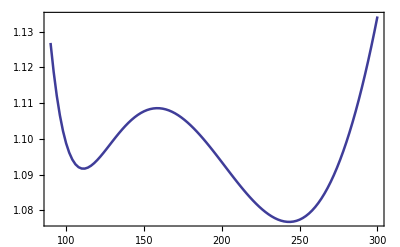

```mathematica
ListPlot[overdiff,Joined->True,BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True]
```

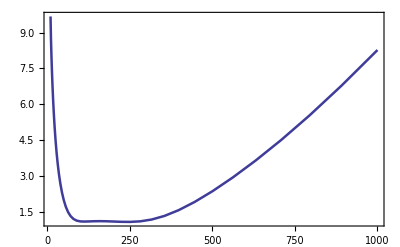

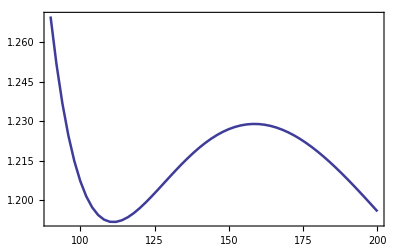

```mathematica
ListPlot[overdiff,Joined->True,BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True]
```

```mathematica
odiff = Map[{#[[1]],Plus @@ (Function[{x},x^2]/@ #[[2]])} &, ss1];
```

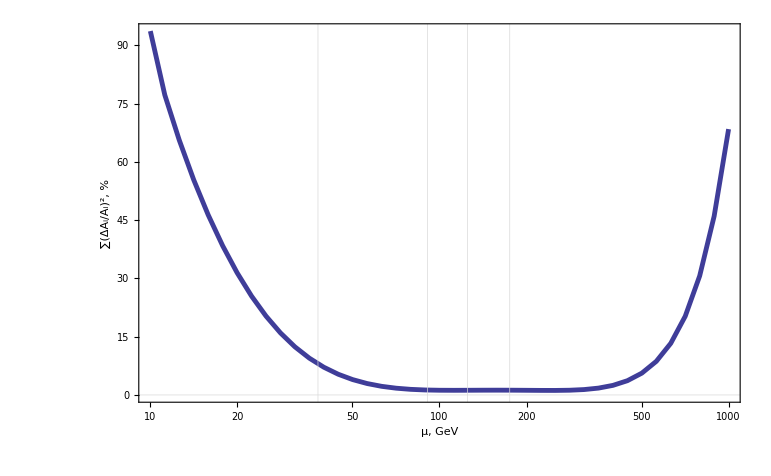

```mathematica
ListLogLinearPlot[ odiff,BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV","∑(ΔA_i/A_i)^2"},GridLines->{{38,91,125,175},{0}},GridLines->{{38,91,125,175},{0}}]
```

```mathematica
names = {"g1","g2","gs","yt","lam","ms"}
```

{g1,g2,gs,yt,lam,ms}

```mathematica
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ ss
```

```mathematica
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ ss1
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ sslog
```

```mathematica
curves[i_]:= Tooltip[{First[#],Abs[ Last[#][[i]]]},names[[i]]] & /@ ss1
```

```mathematica
curves[1]
```

{{10.,2.06745},{11.2202,1.47722},{12.5893,1.11272},{14.1254,0.812972},{15.8489,0.580013},{17.7828,0.402395},{19.9526,0.269252},{22.3872,0.171398},{25.1189,0.101238},{28.1838,0.052514},{31.6228,0.0200548},{35.4813,0.000430586},{39.8107,0.0125253},{44.6684,0.0192409},{50.1187,0.0231244},{56.2341,0.0263434},{63.0957,0.0307514},{70.7946,0.0379389},{79.4328,0.0492707},{89.1251,0.0659126},{100.,0.0888475},{112.202,0.11888},{125.893,0.15663},{141.254,0.202512},{158.489,0.256699},{177.828,0.319061},{199.526,0.389071},{223.872,0.465679},{251.189,0.547115},{281.838,0.630616},{316.228,0.712039},{354.813,0.785306},{398.107,0.841632},{446.684,0.868468},{501.187,0.84808},{562.341,0.755792},{630.957,0.558068},{707.946,0.211105},{794.328,0.338572},{891.251,1.14888},{1000.,2.26953}}

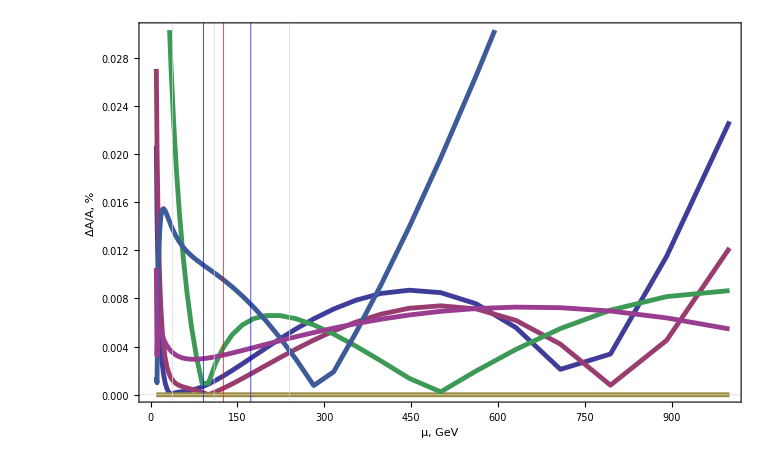

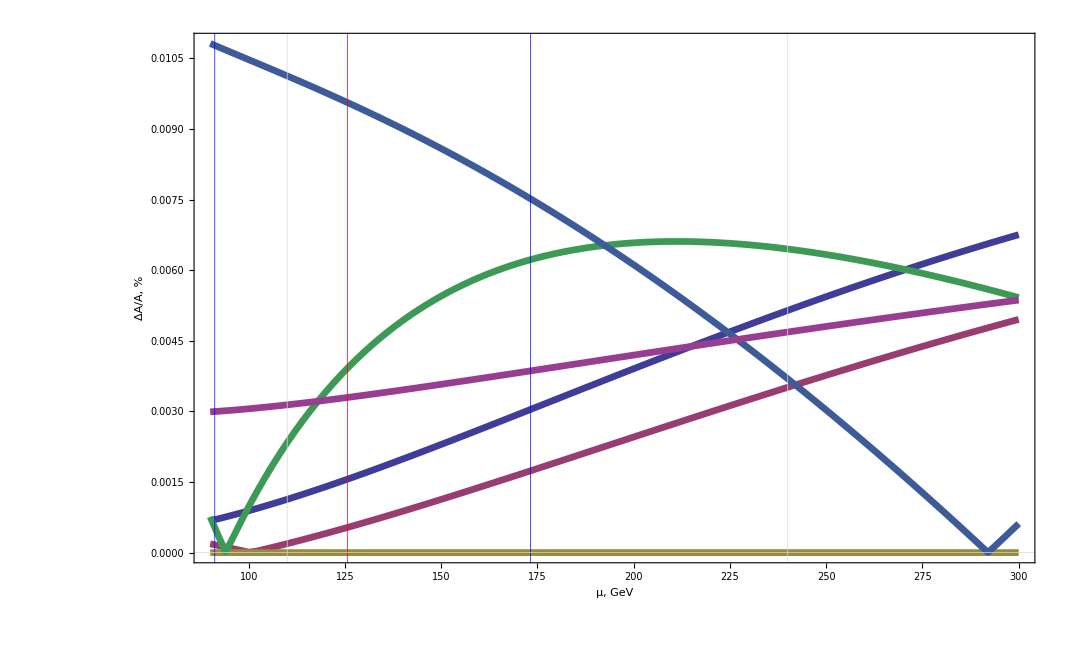

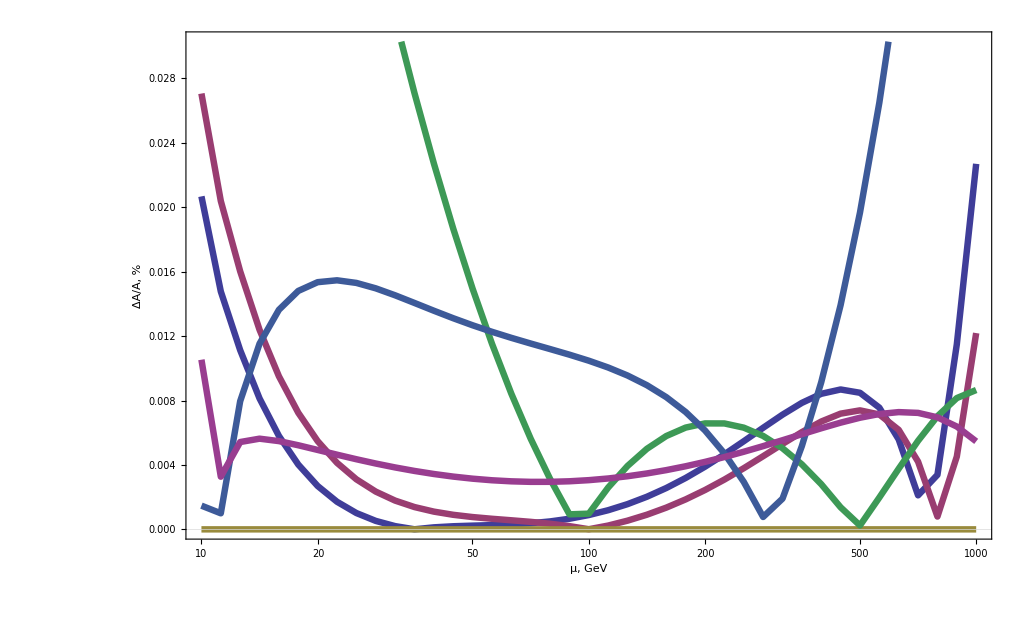

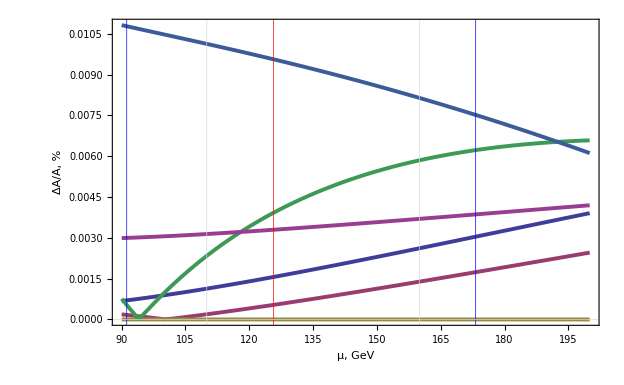

```mathematica
ListPlot[ Table[curves[i],{i,1,6}],BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV","ΔA/A, %"},GridLines->{{38,{PDG`MZ,Blue},110,{PDG`MH,Red},240,{PDG`MT,Blue}},{0}}]
```

Part::partw: Part TraditionalForm`1 of TraditionalForm`{} does not exist.

Part::partw: Part TraditionalForm`2 of TraditionalForm`{} does not exist.

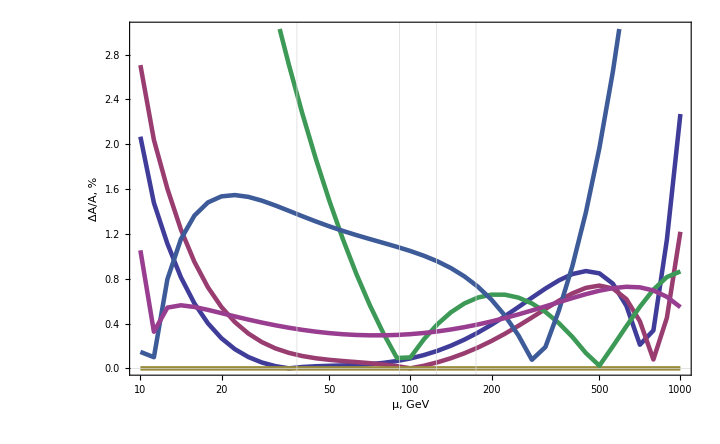

```mathematica
ListLogLinearPlot[ Table[curves[i],{i,1,6}],BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV","ΔA/A, %"},GridLines->{{38,91,125,175},{0}},GridLines->{{38,91,125,175},{0}}]
```

```mathematica
Needs["NumericalCalculus`"]
```

```mathematica
check[obs_,sol_]:= 2Last[Last[sol]]ND[ obs[Sequence @@ ( Most[Last /@ sol]),mu],mu,Last[Last[sol]]]/Symbol["PDG`"  <> ToString[obs]]
```

```mathematica
check[#,s172] & /@ {MW,MZ,MT,MH,GF}
```

{-0.211164,-0.219375,-0.144821,-0.0374918,0.438549}

```mathematica
check[#,s91] & /@ {MW,MZ,MT,MH,GF}
```

{-0.202985,-0.211105,-0.11675,-0.0397194,0.435795}

```mathematica
numericBeta[iscale_,oscale_:-1]:= Module[{sol=sol[iscale][],ss=oscale},If[ss<0,ss=iscale];ss ND[RunSM[Sequence @@ (Last /@ sol),mu],mu,ss]]
```

```mathematica
checkExplicitscale[obs_,scale_]:= Module[{sol = sol[scale][]},(*Print[sol];*)Last[Last[sol]]ND[ obs[Sequence @@ ( Most[Last /@ sol]),mu],mu,Last[Last[sol]],Scale->0.1]/Symbol["PDG`"  <> ToString[obs]]]
```

```mathematica
{#,checkscale[MT,#]} &/@ scales
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

{gp→0.357815,g→0.650613,gs→1.19931,yt→0.978123,lam→0.138141,mu0→131.325,mu→110}

{gp→0.358098,g→0.650296,gs→1.19249,yt→0.974556,lam→0.136176,mu0→131.544,mu→120}

{gp→0.358372,g→0.650026,gs→1.18632,yt→0.971452,lam→0.134388,mu0→131.746,mu→130}

{gp→0.358639,g→0.649796,gs→1.1807,yt→0.968726,lam→0.132748,mu0→131.932,mu→140}

{gp→0.358898,g→0.649599,gs→1.17554,yt→0.966314,lam→0.131232,mu0→132.107,mu→150}

{gp→0.35915,g→0.649429,gs→1.17077,yt→0.964167,lam→0.129821,mu0→132.269,mu→160}

{gp→0.359396,g→0.649284,gs→1.16634,yt→0.962243,lam→0.128501,mu0→132.423,mu→170}

{gp→0.359635,g→0.649159,gs→1.16222,yt→0.960512,lam→0.127259,mu0→132.567,mu→180}

{gp→0.359867,g→0.649051,gs→1.15836,yt→0.958948,lam→0.126087,mu0→132.704,mu→190}

{gp→0.360093,g→0.648959,gs→1.15473,yt→0.957529,lam→0.124975,mu0→132.834,mu→200}

{gp→0.360312,g→0.648879,gs→1.15131,yt→0.956236,lam→0.123918,mu0→132.958,mu→210}

{gp→0.360524,g→0.648809,gs→1.14808,yt→0.955056,lam→0.122909,mu0→133.076,mu→220}

{gp→0.36073,g→0.648749,gs→1.14502,yt→0.953976,lam→0.121944,mu0→133.189,mu→230}

{gp→0.36093,g→0.648696,gs→1.14211,yt→0.952984,lam→0.121018,mu0→133.297,mu→240}

{gp→0.361122,g→0.64865,gs→1.13934,yt→0.952072,lam→0.120128,mu0→133.4,mu→250}

{gp→0.361309,g→0.648608,gs→1.1367,yt→0.951231,lam→0.119271,mu0→133.5,mu→260}

{gp→0.361489,g→0.648571,gs→1.13418,yt→0.950454,lam→0.118443,mu0→133.595,mu→270}

{gp→0.361662,g→0.648537,gs→1.13176,yt→0.949736,lam→0.117643,mu0→133.688,mu→280}

{gp→0.361829,g→0.648506,gs→1.12945,yt→0.94907,lam→0.116868,mu0→133.777,mu→290}

{gp→0.361989,g→0.648476,gs→1.12722,yt→0.948452,lam→0.116117,mu0→133.862,mu→300}

(100 | -0.120675
110 | -0.124764
120 | -0.12853
130 | -0.132025
140 | -0.135288
150 | -0.138352
160 | -0.14124
170 | -0.143974
180 | -0.14657
190 | -0.149042
200 | -0.151401
210 | -0.153658
220 | -0.155822
230 | -0.157899
240 | -0.159896
250 | -0.161818
260 | -0.163671
270 | -0.165458
280 | -0.167183
290 | -0.16885
300 | -0.170462)

```mathematica
ListPlot[{#,checkscale[MT,#]} &/@ scales,Joined->True]
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

{gp→0.357815,g→0.650613,gs→1.19931,yt→0.978123,lam→0.138141,mu0→131.325,mu→110}

{gp→0.358098,g→0.650296,gs→1.19249,yt→0.974556,lam→0.136176,mu0→131.544,mu→120}

{gp→0.358372,g→0.650026,gs→1.18632,yt→0.971452,lam→0.134388,mu0→131.746,mu→130}

{gp→0.358639,g→0.649796,gs→1.1807,yt→0.968726,lam→0.132748,mu0→131.932,mu→140}

{gp→0.358898,g→0.649599,gs→1.17554,yt→0.966314,lam→0.131232,mu0→132.107,mu→150}

{gp→0.35915,g→0.649429,gs→1.17077,yt→0.964167,lam→0.129821,mu0→132.269,mu→160}

{gp→0.359396,g→0.649284,gs→1.16634,yt→0.962243,lam→0.128501,mu0→132.423,mu→170}

{gp→0.359635,g→0.649159,gs→1.16222,yt→0.960512,lam→0.127259,mu0→132.567,mu→180}

{gp→0.359867,g→0.649051,gs→1.15836,yt→0.958948,lam→0.126087,mu0→132.704,mu→190}

{gp→0.360093,g→0.648959,gs→1.15473,yt→0.957529,lam→0.124975,mu0→132.834,mu→200}

{gp→0.360312,g→0.648879,gs→1.15131,yt→0.956236,lam→0.123918,mu0→132.958,mu→210}

{gp→0.360524,g→0.648809,gs→1.14808,yt→0.955056,lam→0.122909,mu0→133.076,mu→220}

{gp→0.36073,g→0.648749,gs→1.14502,yt→0.953976,lam→0.121944,mu0→133.189,mu→230}

{gp→0.36093,g→0.648696,gs→1.14211,yt→0.952984,lam→0.121018,mu0→133.297,mu→240}

{gp→0.361122,g→0.64865,gs→1.13934,yt→0.952072,lam→0.120128,mu0→133.4,mu→250}

{gp→0.361309,g→0.648608,gs→1.1367,yt→0.951231,lam→0.119271,mu0→133.5,mu→260}

{gp→0.361489,g→0.648571,gs→1.13418,yt→0.950454,lam→0.118443,mu0→133.595,mu→270}

{gp→0.361662,g→0.648537,gs→1.13176,yt→0.949736,lam→0.117643,mu0→133.688,mu→280}

{gp→0.361829,g→0.648506,gs→1.12945,yt→0.94907,lam→0.116868,mu0→133.777,mu→290}

{gp→0.361989,g→0.648476,gs→1.12722,yt→0.948452,lam→0.116117,mu0→133.862,mu→300}

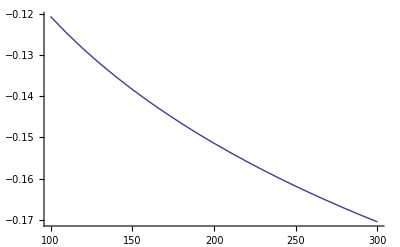

```mathematica
ListPlot[{#,checkscale[MT,#]} &/@ scales,Joined->True]
```

```mathematica
ListPlot[{#,checkscale[MZ,#]} &/@ scales,Joined->True]
```

{gp→0.357524,g→0.650985,gs→1.20692,yt→0.982265,lam→0.140325,mu0→131.084,mu→100}

{gp→0.357815,g→0.650613,gs→1.19931,yt→0.978123,lam→0.138141,mu0→131.325,mu→110}

{gp→0.358098,g→0.650296,gs→1.19249,yt→0.974556,lam→0.136176,mu0→131.544,mu→120}

{gp→0.358372,g→0.650026,gs→1.18632,yt→0.971452,lam→0.134388,mu0→131.746,mu→130}

{gp→0.358639,g→0.649796,gs→1.1807,yt→0.968726,lam→0.132748,mu0→131.932,mu→140}

{gp→0.358898,g→0.649599,gs→1.17554,yt→0.966314,lam→0.131232,mu0→132.107,mu→150}

{gp→0.35915,g→0.649429,gs→1.17077,yt→0.964167,lam→0.129821,mu0→132.269,mu→160}

{gp→0.359396,g→0.649284,gs→1.16634,yt→0.962243,lam→0.128501,mu0→132.423,mu→170}

{gp→0.359635,g→0.649159,gs→1.16222,yt→0.960512,lam→0.127259,mu0→132.567,mu→180}

{gp→0.359867,g→0.649051,gs→1.15836,yt→0.958948,lam→0.126087,mu0→132.704,mu→190}

{gp→0.360093,g→0.648959,gs→1.15473,yt→0.957529,lam→0.124975,mu0→132.834,mu→200}

{gp→0.360312,g→0.648879,gs→1.15131,yt→0.956236,lam→0.123918,mu0→132.958,mu→210}

{gp→0.360524,g→0.648809,gs→1.14808,yt→0.955056,lam→0.122909,mu0→133.076,mu→220}

{gp→0.36073,g→0.648749,gs→1.14502,yt→0.953976,lam→0.121944,mu0→133.189,mu→230}

{gp→0.36093,g→0.648696,gs→1.14211,yt→0.952984,lam→0.121018,mu0→133.297,mu→240}

{gp→0.361122,g→0.64865,gs→1.13934,yt→0.952072,lam→0.120128,mu0→133.4,mu→250}

{gp→0.361309,g→0.648608,gs→1.1367,yt→0.951231,lam→0.119271,mu0→133.5,mu→260}

{gp→0.361489,g→0.648571,gs→1.13418,yt→0.950454,lam→0.118443,mu0→133.595,mu→270}

{gp→0.361662,g→0.648537,gs→1.13176,yt→0.949736,lam→0.117643,mu0→133.688,mu→280}

{gp→0.361829,g→0.648506,gs→1.12945,yt→0.94907,lam→0.116868,mu0→133.777,mu→290}

{gp→0.361989,g→0.648476,gs→1.12722,yt→0.948452,lam→0.116117,mu0→133.862,mu→300}

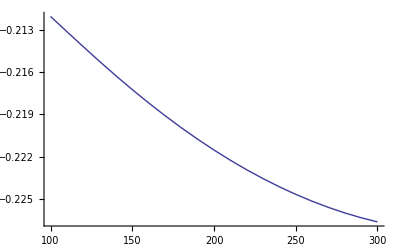

```mathematica
RunSM[Sequence @@ (Last /@ s91), PDG`MT]
```

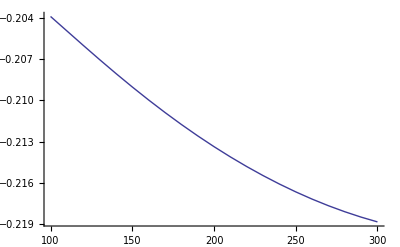

```mathematica
ListPlot[{#,checkscale[MW,#]} &/@ scales,Joined->True]
```

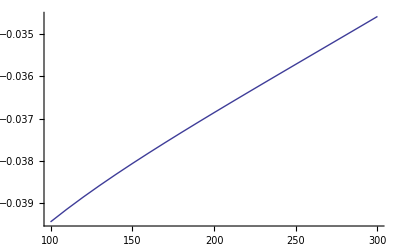

```mathematica
ListPlot[{#,checkscale[MH,#]} &/@ scales,Joined->True]
```

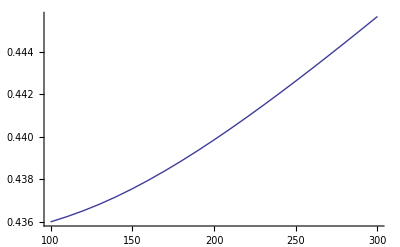

```mathematica
ListPlot[{#,checkscale[GF,#]} &/@ scales,Joined->True]
```

```mathematica
rr = RunSM[Sequence @@ (Last /@ s91), PDG`MT]
```

{0.358557661771828428,0.6479785593759323419,1.165002622973601411,0.9497487829378230192,0.127719318006899446,132.2994282778492337,173.210000000000008}

```mathematica
PDG`MT  ND[RunSM[Sequence @@ (Last /@ s91), mu],mu,PDG`MT]
```

{0.00203502,-0.00525068,-0.072294,-0.0538173,-0.0215114,2.14155,173.21}

```mathematica
nr = (Last /@ s172)
```

{0.359473,0.649242,1.16499,0.961668,0.128094,132.47,173.21}

```mathematica
100(1-nr/rr)
```

{-0.255378,-0.194954,0.00125722,-1.25499,-0.293387,-0.128929,0.}

```mathematica
smt10 = sol[10 PDG`MT][];
```

```mathematica
smtd10 = sol[PDG`MT/10][];
```

```mathematica
numericBeta[PDG`MZ,PDG`MT]
```

{0.00203502,-0.00525068,-0.072294,-0.0538173,-0.0215114,2.14155,173.21}

```mathematica
numericBeta[PDG`MZ,PDG`MZ]
```

{0.00201616,-0.00531678,-0.0821164,-0.0610575,-0.0246032,2.37762,91.1876}

```mathematica
Clear[NumGrad]
```

```mathematica
NumGrad[obs_,scale_,s_:0.1]:= Module[{sl = sol[scale][],pars,tpars},pars = Most[ Last /@ sl];tpars =Table[{ReplacePart[pars,i->xxxx],pars[[i]]},{i,Length[pars]}]; Map[ND[obs[Sequence @@ First[#], scale],xxxx,Last[#],Scale->s] &,tpars]]
```

```mathematica
NumGrad[MH,PDG`MZ].Most[numericBeta[PDG`MZ]]
```

1.00273-0.000969167 (1/31 (1/15 (1/7 (1/3 (1. (-1. nan-125.7)+529.317)+362.252)-409.271)+879.867)-1753.65)

```mathematica
sol[PDG`MZ][]
```

{gp→0.357258,g→0.651369,gs→1.21442,yt→0.986513,lam→0.142474,mu0→130.852,mu→91.1876}

```mathematica
NumGrad1[MH,PDG`MZ]/PDG`MH //TableForm
```

0.00296713
0.0149058
0.00547449
-0.218005
0.409963
0.00779402

0.372968
1.87366
0.688143
-27.4032
51.5371
0.979708

```mathematica
NumGrad1[obs_,scale_]:= Module[{sl = sol[scale][],pars,tpars},pars = Most[ Last /@ sl];tpars =Table[{ReplacePart[pars,i->xxxx],pars[[i]]},{i,Length[pars]}]; Map[ND[obs[Sequence @@ First[#], scale],xxxx,Last[#],Scale->0.1] &,tpars]]
```

```mathematica
checkImplicitScale[obs_,scale_]:= Module[{sol = sol[scale][]},(*Print[sol];*)Most[numericBeta[scale]]. NumGrad[obs,scale]/Symbol["PDG`"  <> ToString[obs]]]
```

```mathematica
checkImplicitScale[MZ,PDG`MZ]+x checkExplicitscale[MZ,PDG`MZ]
```

0.104869-0.105553 x

-0.000683953

```mathematica
(checkImplicitScale[#,PDG`MZ]+x checkExplicitscale[#,PDG`MZ]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.100803-0.101493 x
0.104869-0.105553 x
0.0457875-0.0583751 x
0.0212328-0.0198597 x
0.217897 x-0.219877

```mathematica
(checkImplicitScale[#,PDG`MZ]+x checkExplicitscale[#,PDG`MZ]) &/@ {MW,MZ,MT,MH,GF}  /. x->1//TableForm
```

-0.000690165
-0.000683953
-0.0125876
0.0013731
-0.00197953

```mathematica
(checkImplicitScale[#,PDG`MT]+x checkExplicitscale[#,PDG`MT]) &/@ {MW,MZ,MT,MH,GF} //TableForm
```

0.106112-0.105582 x
0.110218-0.109687 x
0.0544809-0.0724107 x
0.0207942-0.0187459 x
0.219274 x-0.229489

```mathematica
(checkImplicitScale[#,PDG`MT]+x checkExplicitscale[#,PDG`MT]) &/@ {MW,MZ,MT,MH,GF} /. x->1//TableForm
```

0.000529465
0.000530784
-0.0179298
0.00204835
-0.0102145

0.000529465
0.000530784
-0.0179298
0.00204835
-0.0102145

```mathematica
LogMuDerivative[obs_,scale_]:= 100*(checkImplicitScale[obs,scale]+ checkExplicitscale[obs,scale]); (* d Log/ d Log[mu], in percents *)
```

```mathematica
LogMuDerivative[MT,PDG`MZ]
```

-1.25876

0.000529465

```mathematica
MWscaledep ={#, LogMuDerivative[MW,#]} & /@ scales;
MZscaledep ={#,  LogMuDerivative[MZ,#]} & /@ scales;
MTscaledep = {#, LogMuDerivative[MT,#] }& /@ scales;
MHscaledep ={#,  LogMuDerivative[MH,#]} & /@ scales;
GFscaledep = {#, LogMuDerivative[GF,#]} & /@ scales;
```

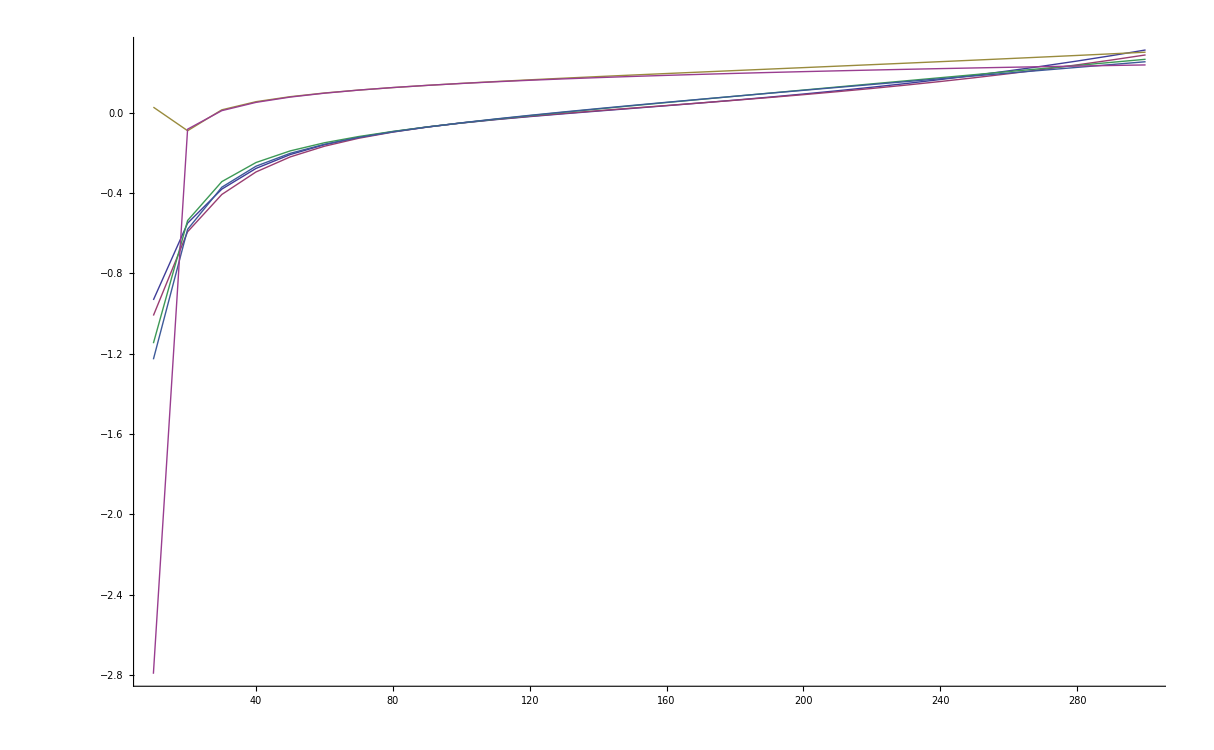

```mathematica
ListPlot[{MZscaledep,MWscaledep,MHscaledep,mZscaledep,mWscaledep,mHscaledep},Joined->True]
```

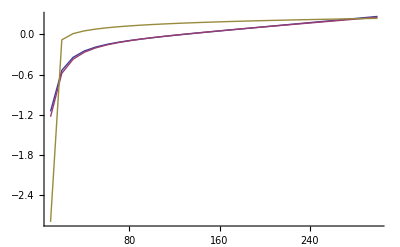

```mathematica
ListPlot[{mZscaledep,mWscaledep,mHscaledep},Joined->True]
```

```mathematica
xxx=Tooltip[GFscaledep,"G_F"];
```

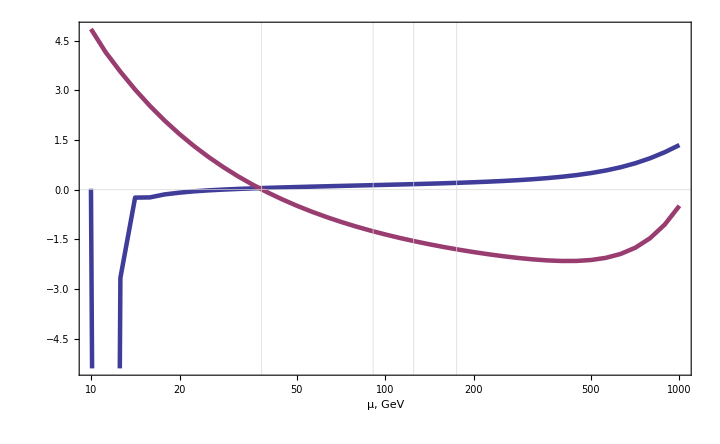

```mathematica
ListLogLinearPlot[{Tooltip[MHscaledep,"M_H"],Tooltip[MTscaledep,"M_t"]},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV",""},GridLines->{{38,91,125,175},{0}},ImageSize->{72 10,72 7}]
```

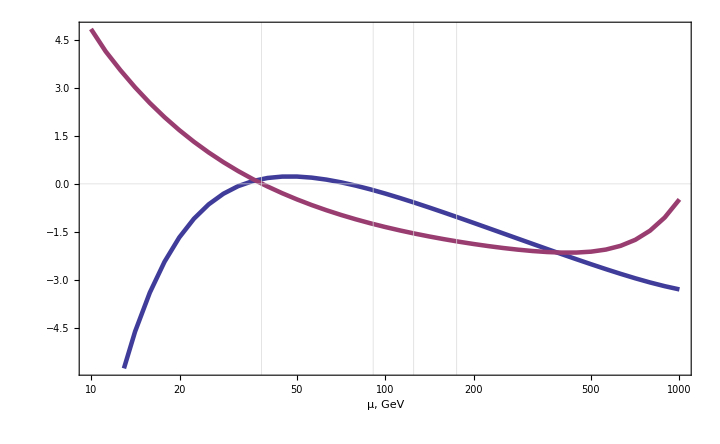

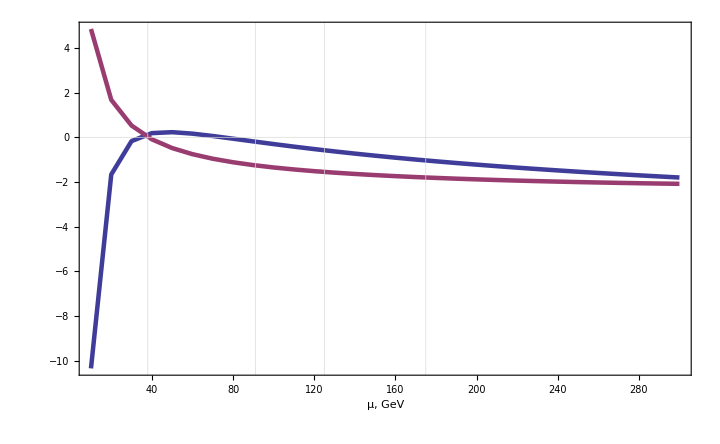

```mathematica
ListLogLinearPlot[{Tooltip[GFscaledep,"G_F"],Tooltip[MTscaledep,"M_t"]},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV",""},GridLines->{{38,91,125,175},{0}},ImageSize->{72 10,72 7}]
```

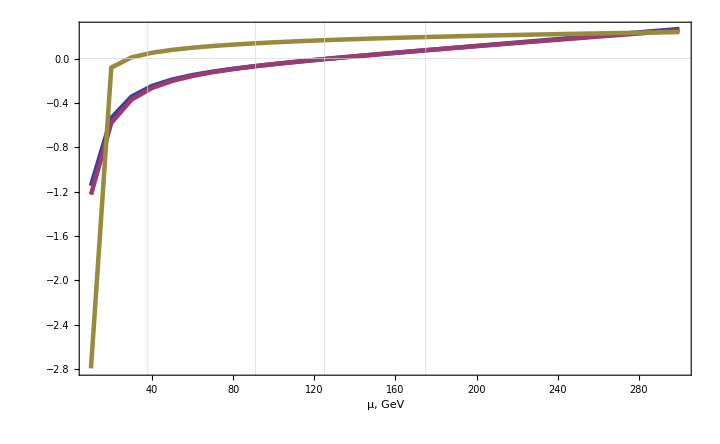

```mathematica
ListPlot[{mZscaledep,mWscaledep,mHscaledep},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,Joined->True,FrameLabel->{"μ, GeV",""},GridLines->{{38,91,125,175},{0}},ImageSize->{72 10,72 7}]
```

```mathematica
xxx //FullForm
```

Tooltip[List[List[10,-10.3482],List[20,-1.66533],List[30,-0.169803],List[40,0.187077],List[50,0.229603],List[60,0.163801],List[70,0.0579141],List[80,-0.0616098],List[90,-0.183574],List[100,-0.303058],List[110,-0.417939],List[120,-0.527412],List[130,-0.631304],List[140,-0.72975],List[150,-0.823024],List[160,-0.911458],List[170,-0.995398],List[180,-1.07518],List[190,-1.15112],List[200,-1.22351],List[210,-1.29263],List[220,-1.35871],List[230,-1.42199],List[240,-1.48265],List[250,-1.54089],List[260,-1.59686],List[270,-1.65072],List[280,-1.70261],List[290,-1.75265],List[300,-1.80095]],"G_F"]

```mathematica
ListPlot[{Tooltip[GFscaledep,"G_F"],Tooltip[MTscaledep,"M_t"],gFscaledep,mTscaledep},Joined->True]//FullForm
```

Graphics[List[Hue[0.67,0.6,0.6],Line[List[List[10.,-10.3482],List[20.,-1.66533],List[30.,-0.169803],List[40.,0.187077],List[50.,0.229603],List[60.,0.163801],List[70.,0.0579141],List[80.,-0.0616098],List[90.,-0.183574],List[100.,-0.303058],List[110.,-0.417939],List[120.,-0.527412],List[130.,-0.631304],List[140.,-0.72975],List[150.,-0.823024],List[160.,-0.911458],List[170.,-0.995398],List[180.,-1.07518],List[190.,-1.15112],List[200.,-1.22351],List[210.,-1.29263],List[220.,-1.35871],List[230.,-1.42199],List[240.,-1.48265],List[250.,-1.54089],List[260.,-1.59686],List[270.,-1.65072],List[280.,-1.70261],List[290.,-1.75265],List[300.,-1.80095]]],Hue[0.906068,0.6,0.6],Line[List[List[10.,4.85033],List[20.,1.67662],List[30.,0.526149],List[40.,-0.0905856],List[50.,-0.481825],List[60.,-0.755261],List[70.,-0.958881],List[80.,-1.11747],List[90.,-1.24519],List[100.,-1.35074],List[110.,-1.43977],List[120.,-1.51612],List[130.,-1.58248],List[140.,-1.64081],List[150.,-1.69256],List[160.,-1.73884],List[170.,-1.78048],List[180.,-1.81816],List[190.,-1.8524],List[200.,-1.88364],List[210.,-1.91221],List[220.,-1.9384],List[230.,-1.96243],List[240.,-1.98452],List[250.,-2.00481],List[260.,-2.02345],List[270.,-2.04054],List[280.,-2.0562],List[290.,-2.07049],List[300.,-2.0835]]],Hue[0.142136,0.6,0.6],Line[List[List[10.,-10.4684],List[20.,-1.66176],List[30.,-0.148625],List[40.,0.206153],List[50.,0.242085],List[60.,0.170147],List[70.,0.060019],List[80.,-0.0616066],List[90.,-0.183682],List[100.,-0.301544],List[110.,-0.41334],List[120.,-0.518507],List[130.,-0.617082],List[140.,-0.709376],List[150.,-0.79581],List[160.,-0.87684],List[170.,-0.952912],List[180.,-1.02445],List[190.,-1.09184],List[200.,-1.15543],List[210.,-1.21555],List[220.,-1.27249],List[230.,-1.3265],List[240.,-1.37781],List[250.,-1.42664],List[260.,-1.47317],List[270.,-1.51757],List[280.,-1.56],List[290.,-1.60059],List[300.,-1.63947]]],Hue[0.378204,0.6,0.6],Line[List[List[10.,4.75517],List[20.,1.67238],List[30.,0.531523],List[40.,-0.0844164],List[50.,-0.47712],List[60.,-0.752368],List[70.,-0.95749],List[80.,-1.11706],List[90.,-1.24518],List[100.,-1.3506],List[110.,-1.43903],List[120.,-1.51436],List[130.,-1.57938],List[140.,-1.63611],List[150.,-1.68606],List[160.,-1.73038],List[170.,-1.76999],List[180.,-1.8056],List[190.,-1.83778],List[200.,-1.867],List[210.,-1.89364],List[220.,-1.91802],List[230.,-1.94041],List[240.,-1.96103],List[250.,-1.98008],List[260.,-1.99771],List[270.,-2.01407],List[280.,-2.02929],List[290.,-2.04346],List[300.,-2.0567]]]],List[Rule[AspectRatio,Power[GoldenRatio,-1]],Rule[Axes,True],Rule[PlotRange,Automatic],Rule[PlotRangeClipping,True]]]

```mathematica
ListPlot[{Tooltip[GFscaledep,"G_F"],Tooltip[MTscaledep,"M_t"],gFscaledep,mTscaledep},Joined->True]/.Tooltip[{color___,line_},tip_]:>{color,line,Text[tip,line[[1,-100]],BaseStyle->20,Background->White]}
```

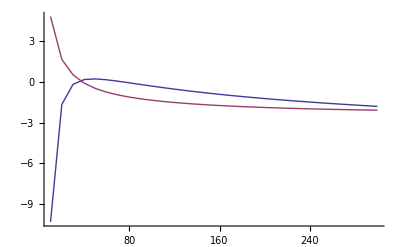

```mathematica
ListPlot[{GFscaledep,MTscaledep},Joined->True]
```

```mathematica
MZscaledep
```

(10 | -0.932013
20 | -0.549905
30 | -0.380423
40 | -0.277277
50 | -0.208339
60 | -0.159261
70 | -0.122578
80 | -0.093998
90 | -0.0708682
100 | -0.051454
110 | -0.0345683
120 | -0.0193673
130 | -0.00523155
140 | 0.00830686
150 | 0.0216104
160 | 0.0349662
170 | 0.0486069
180 | 0.0627245
190 | 0.0774803
200 | 0.0930125
210 | 0.109441
220 | 0.126872
230 | 0.145401
240 | 0.165112
250 | 0.186087
260 | 0.208396
270 | 0.232111
280 | 0.257294
290 | 0.284008
300 | 0.312313)

```mathematica
LogMuDerivativeWithRunning[iscale_][obs_,scale_]:= Module[{sl = sol[iscale][],dummy},dummy[x_?NumericQ]:= Module[{ppp=RunSM[Sequence @@ (Last /@ sl),x]},obs[ Sequence @@ ppp]];
scale/Symbol["PDG`"  <> ToString[obs]] *ND[dummy[xxx],xxx,scale,Scale->0.1]]
```

```mathematica
mttestdep = {#,100*LogMuDerivativeWithRunning[PDG`MZ][MT,#]} &/@ scales;
```

(100 | -1.3506
110 | -1.43903
120 | -1.51436
130 | -1.57938
140 | -1.63611
150 | -1.68606
160 | -1.73038
170 | -1.76999
180 | -1.8056
190 | -1.83778
200 | -1.867
210 | -1.89364
220 | -1.91802
230 | -1.94041
240 | -1.96103
250 | -1.98008
260 | -1.99771
270 | -2.01407
280 | -2.02929
290 | -2.04346
300 | -2.0567)

```mathematica
mttest1dep = {#,100*LogMuDerivativeWithRunning[PDG`MT][MT,#]} &/@ scales;
```

```mathematica
mttest2dep = {#,100*LogMuDerivativeWithRunning[300][MT,#]} &/@ scales;
```

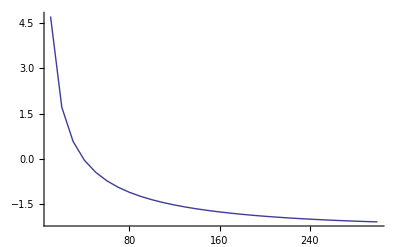

```mathematica
ListPlot[mttest2dep,Joined->True]
```

```mathematica
N
```

```mathematica
MTscaledep
```

(100 | -1.35074
110 | -1.43977
120 | -1.51612
130 | -1.58248
140 | -1.64081
150 | -1.69256
160 | -1.73884
170 | -1.78048
180 | -1.81816
190 | -1.8524
200 | -1.88364
210 | -1.91221
220 | -1.9384
230 | -1.96243
240 | -1.98452
250 | -2.00481
260 | -2.02345
270 | -2.04054
280 | -2.0562
290 | -2.07049
300 | -2.0835)

```mathematica
MTscaledep-mttestdep
```

(0 | -0.000142824
0 | -0.000748648
0 | -0.00175807
0 | -0.0030994
0 | -0.00470418
0 | -0.00650867
0 | -0.00845417
0 | -0.010487
0 | -0.0125578
0 | -0.0146217
0 | -0.016637
0 | -0.0185654
0 | -0.0203714
0 | -0.0220217
0 | -0.0234853
0 | -0.0247329
0 | -0.0257366
0 | -0.0264703
0 | -0.0269086
0 | -0.0270276
0 | -0.0268038)

```mathematica
mWscaledep ={#, 100 LogMuDerivativeWithRunning[PDG`MZ][MW,#]} & /@ scales;
mZscaledep ={#, 100  LogMuDerivativeWithRunning[PDG`MZ][MZ,#]} & /@ scales;
mTscaledep = {#, 100 LogMuDerivativeWithRunning[PDG`MZ][MT,#] }& /@ scales;
mHscaledep ={#,  100 LogMuDerivativeWithRunning[PDG`MZ][MH,#]} & /@ scales;
gFscaledep = {#, 100 LogMuDerivativeWithRunning[PDG`MZ][GF,#]} & /@ scales;
```

```mathematica
ScaleDep[iscale_][obs_,scale_]:= Module[{sl = sol[iscale][],dummy},dummy[x_?NumericQ]:= Module[{ppp=RunSM[Sequence @@ (Last /@ sl),x]},obs[ Sequence @@ ppp]];
dummy[scale]]
```

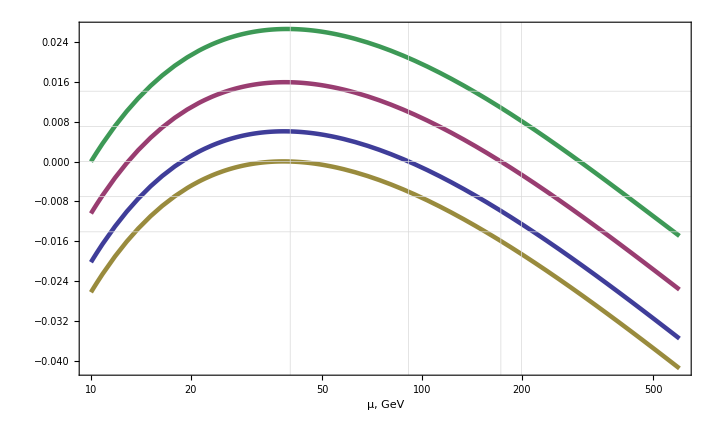

```mathematica
LogLinearPlot[{ScaleDep[PDG`MZ][MT,x]/PDG`MT-1,ScaleDep[PDG`MT][MT,x]/PDG`MT-1,ScaleDep[40][MT,x]/PDG`MT-1,ScaleDep[300][MT,x]/PDG`MT-1},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{0,-PDG`dMT/PDG`MT,-2PDG`dMT/PDG`MT,+PDG`dMT/PDG`MT,+2PDG`dMT/PDG`MT}},ImageSize->{72 10,72 7}]
```

```mathematica
EstimateTheorUncertainty[Sequence @@ (Last /@ sol[PDG`MZ][])]
```

{0.3586626304561123155,0.6477079655285805314,1.161293213030017322,0.946987214269128843,0.1266158332265555917,132.4093967768038963,182.3752000000000066,2}

(91.18760000000000717 | 0.0000224608564930277 | 0.0009477878405394346
80.38499999999996721 | 0.0000296293090979903 | 0.0009942871228845826
173.20999999999996 | -0.01081840760123 | 0.0057604775843616
125.7000000000000184 | 0.00116111628925567 | -0.000719608686289938
0.00001166378700000000619 | -0.004235520878445559 | -0.000629517918260365)

```mathematica
EstimateTheorUncertainty[Sequence @@ (Last /@ sol[PDG`MT][])]
```

{0.3609021115346426776,0.6456062317682658074,1.117952645156373051,0.9265856779548876017,0.1132472843757865877,133.9158922969686749,346.4200000000000159,2}

(91.18759999999986424 | 0.001323846895572077 | 0.000134571831976795
80.3849999999998958 | 0.001254615626271249 | 0.000128187744177326
173.2099999999997785 | -0.013686736834933301 | 0.01056009139671077
125.7000000000000205 | 0.001672126867998785 | -0.00117354266176821
0.00001166378700000001095 | -0.01011129689358631 | 0.003986855255409544)

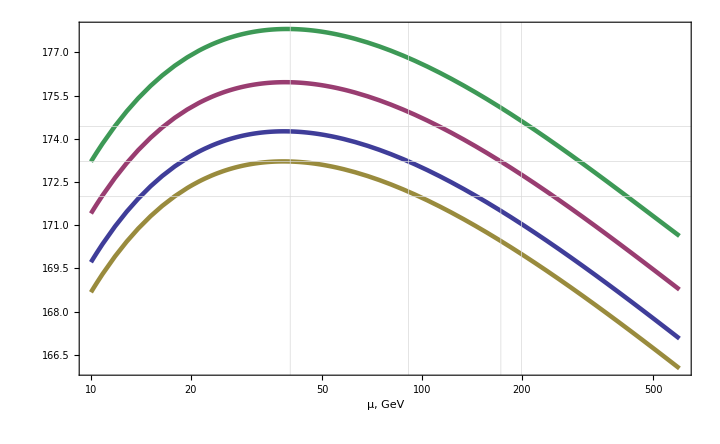

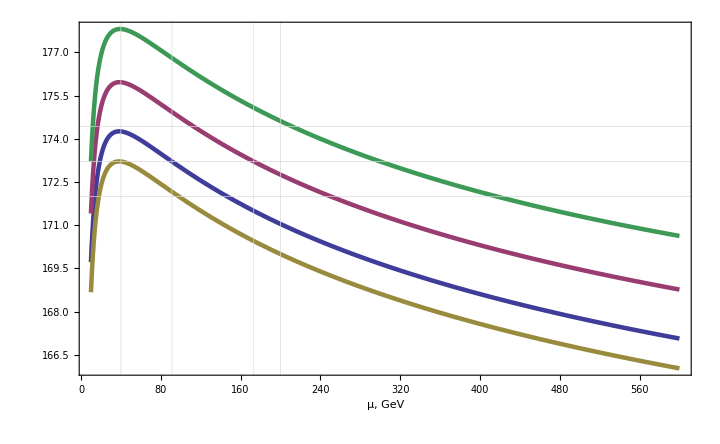

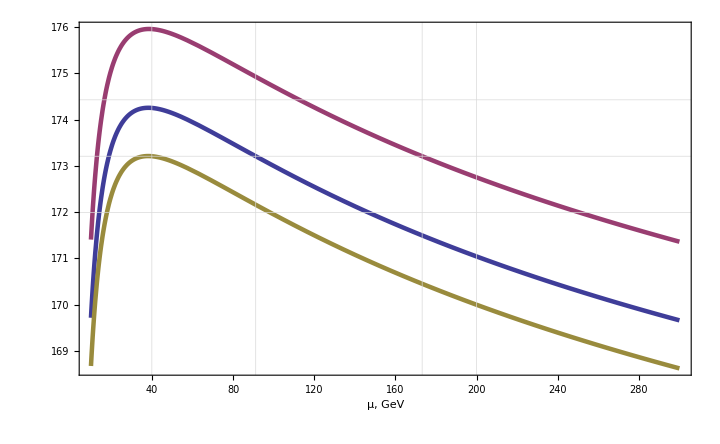

```mathematica
LogLinearPlot[{ScaleDep[PDG`MZ][MT,x],ScaleDep[PDG`MT][MT,x],ScaleDep[40][MT,x],ScaleDep[300][MT,x]},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{PDG`MT,PDG`MT-PDG`dMT,PDG`MT+PDG`dMT}},ImageSize->{72 10,72 7}]
```

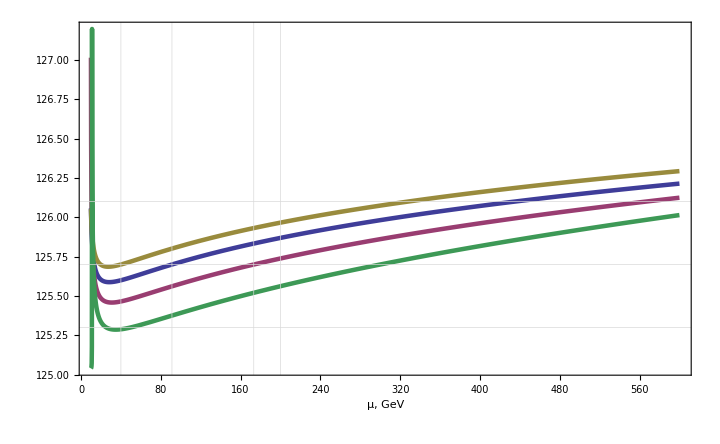

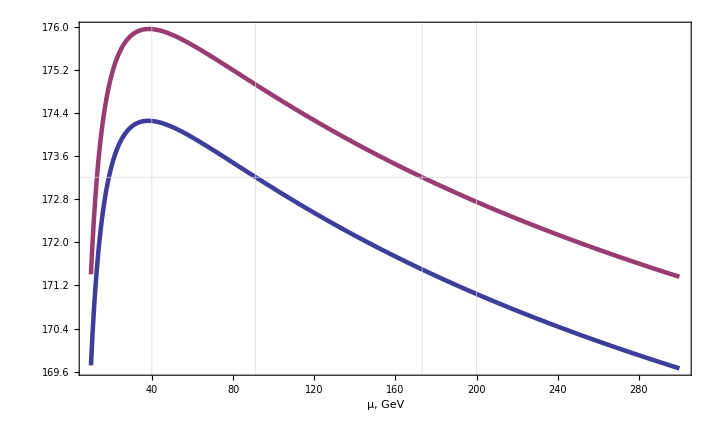

```mathematica
Plot[{ScaleDep[PDG`MZ][MH,x],ScaleDep[PDG`MT][MH,x],ScaleDep[40][MH,x],ScaleDep[300][MH,x]},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{PDG`MH,PDG`MH-PDG`dMH,PDG`MH+PDG`dMH}},ImageSize->{72 10,72 7}]
```

FindRoot::nlnum: The function value TraditionalForm`{-91.1876 + MZ(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -80.385 + MW(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -173.21 + MT(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -125.7 + MH(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -0.0000116638 + GF(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), 0.108301  - 1.\ RunQCD(x, 0.1185, 91.1876, 4., 173.21)}
 is not a list of numbers with dimensions TraditionalForm`{6} at TraditionalForm`{gp, g, gs, yt, lam, mu0} = TraditionalForm`{0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03}.

Join::heads: Heads TraditionalForm`FindRoot and TraditionalForm`List at positions TraditionalForm`1 and TraditionalForm`2 are expected to be the same.

FindRoot::nlnum: The function value TraditionalForm`{-91.1876 + MZ(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -80.385 + MW(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -173.21 + MT(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -125.7 + MH(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -0.0000116638 + GF(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), 0.108301  - 1.\ RunQCD(x, 0.1185, 91.1876, 4., 173.21)}
 is not a list of numbers with dimensions TraditionalForm`{6} at TraditionalForm`{gp, g, gs, yt, lam, mu0} = TraditionalForm`{0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03}.

Join::heads: Heads TraditionalForm`FindRoot and TraditionalForm`List at positions TraditionalForm`1 and TraditionalForm`2 are expected to be the same.

FindRoot::nlnum: The function value TraditionalForm`{-91.1876 + MZ(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -80.385 + MW(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -173.21 + MT(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -125.7 + MH(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), -0.0000116638 + GF(0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03, x, 2.), 0.108301  - 1.\ RunQCD(x, 0.1185, 91.1876, 4., 173.21)}
 is not a list of numbers with dimensions TraditionalForm`{6} at TraditionalForm`{gp, g, gs, yt, lam, mu0} = TraditionalForm`{0.357561, 0.64822, 1.1666, 0.93558, 0.12711, 132.03}.

General::stop: Further output of FindRoot :: nlnum will be suppressed during this calculation.

Join::heads: Heads TraditionalForm`FindRoot and TraditionalForm`List at positions TraditionalForm`1 and TraditionalForm`2 are expected to be the same.

General::stop: Further output of Join :: heads will be suppressed during this calculation.

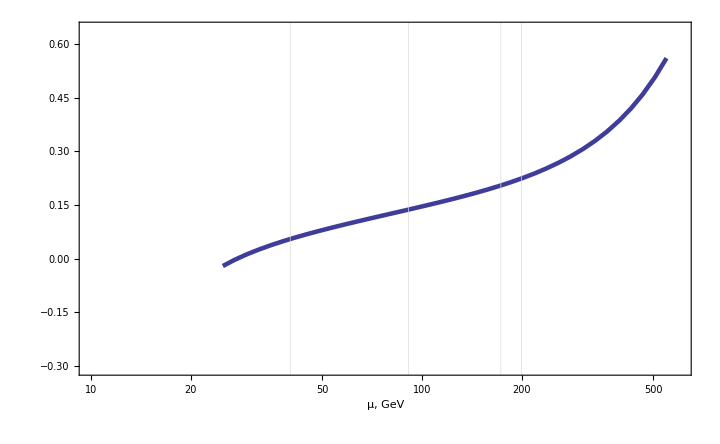

```mathematica
LogLinearPlot[{LogMuDerivative[MH,x],LogMuDerivative[MH,x],LogMuDerivative[MH,x],LogMuDerivative[MH,x]},{x,10,600},BaseStyle->20,Background->None,PlotStyle->Thickness[0.0045],Axes->False,Frame->True,FrameLabel->{"μ, GeV",""},GridLines->{{40,PDG`MZ,PDG`MT,200},{-PDG`dMH,PDG`MH/PDG`MH}},ImageSize->{72 10,72 7}]
```